# Discrete Map

## Logistic Map

```mathematica
G[λ_,x_]:=λ x(1-x)
```

```mathematica
limpoints[λ_]:=NestList[G[λ,#]&,RandomReal[{0,1}],500][[301;;500]]
```

```mathematica
points[λ_,L_]:=Table[Graphics[{PointSize->Tiny,Red,Point[{λ,L[[j]]}]},Axes->True,AxesLabel->{a}],{j,1,Length[L]}]
```

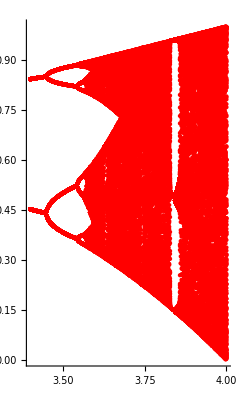

```mathematica
diagorbitas=Show[Table[points[λ,limpoints[λ]],{λ,3.4,4,0.0025}]]
```

## Mandelbrot Set

```mathematica
f[c_,maxiter_Integer:10^3]:=Abs[NestWhile[#^2+c&,0,Abs[#]<2&,1 (*m*),maxiter]]<2 (*Para revisar si el numero debe ser considerado *)
ArrayPlot[Table[Boole[f[N[x+I y],10^3]],{y,-2,2,1/100},{x,-2,1,1/100}]]
```

-Graphics-